# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

700

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
$SAVEMXQ=False
```

False

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results

```mathematica
FileNames[]
```

{run-1,run-10,run-100,run-101,run-102,run-103,run-104,run-105,run-106,run-107,run-108,run-109,run-11,run-110,run-111,run-112,run-113,run-114,run-115,run-116,run-117,run-118,run-119,run-12,run-120,run-121,run-122,run-123,run-124,run-125,run-126,run-127,run-128,run-129,run-13,run-130,run-131,run-132,run-133,run-134,run-135,run-136,run-137,run-138,run-139,run-14,run-140,run-141,run-142,run-143,run-144,run-145,run-146,run-147,run-148,run-149,run-15,run-150,run-151,run-152,run-153,run-154,run-155,run-156,run-157,run-158,run-159,run-16,run-160,run-161,run-162,run-163,run-164,run-165,run-166,run-167,run-168,run-169,run-17,run-170,run-171,run-172,run-173,run-174,run-175,run-176,run-177,run-178,run-179,run-18,run-180,run-181,run-182,run-183,run-184,run-185,run-186,run-187,run-188,run-189,run-19,run-190,run-191,run-192,run-193,run-194,run-195,run-196,run-197,run-198,run-199,run-2,run-20,run-200,run-201,run-202,run-203,run-204,run-205,run-206,run-207,run-208,run-209,run-21,run-210,run-211,run-212,run-213,run-214,run-215,run-216,run-217,run-218,run-219,run-22,run-220,run-221,run-222,run-223,run-224,run-225,run-226,run-227,run-228,run-229,run-23,run-230,run-231,run-232,run-233,run-234,run-235,run-236,run-237,run-238,run-239,run-24,run-240,run-241,run-242,run-243,run-244,run-245,run-246,run-247,run-248,run-249,run-25,run-250,run-251,run-252,run-253,run-254,run-255,run-256,run-257,run-258,run-259,run-26,run-260,run-261,run-262,run-263,run-264,run-265,run-266,run-267,run-268,run-269,run-27,run-270,run-271,run-272,run-273,run-274,run-275,run-276,run-277,run-278,run-279,run-28,run-280,run-281,run-282,run-283,run-284,run-285,run-286,run-287,run-288,run-289,run-29,run-290,run-291,run-292,run-293,run-294,run-295,run-296,run-297,run-298,run-299,run-3,run-30,run-300,run-301,run-302,run-303,run-304,run-305,run-306,run-307,run-308,run-309,run-31,run-310,run-311,run-312,run-313,run-314,run-315,run-316,run-317,run-318,run-319,run-32,run-320,run-321,run-322,run-323,run-324,run-325,run-326,run-327,run-328,run-329,run-33,run-330,run-331,run-332,run-333,run-334,run-335,run-336,run-337,run-338,run-339,run-34,run-340,run-341,run-342,run-343,run-344,run-345,run-346,run-347,run-348,run-349,run-35,run-350,run-351,run-352,run-353,run-354,run-355,run-356,run-357,run-358,run-359,run-36,run-360,run-361,run-362,run-363,run-364,run-365,run-366,run-367,run-368,run-369,run-37,run-370,run-371,run-372,run-373,run-374,run-375,run-376,run-377,run-378,run-379,run-38,run-380,run-381,run-382,run-383,run-384,run-385,run-386,run-387,run-388,run-389,run-39,run-390,run-391,run-392,run-393,run-394,run-395,run-396,run-397,run-398,run-399,run-4,run-40,run-400,run-401,run-402,run-403,run-404,run-405,run-406,run-407,run-408,run-409,run-41,run-410,run-411,run-412,run-413,run-414,run-415,run-416,run-417,run-418,run-419,run-42,run-420,run-421,run-422,run-423,run-424,run-425,run-426,run-427,run-428,run-429,run-43,run-430,run-431,run-432,run-433,run-434,run-435,run-436,run-437,run-438,run-439,run-44,run-440,run-441,run-442,run-443,run-444,run-445,run-446,run-447,run-448,run-449,run-45,run-450,run-46,run-47,run-48,run-49,run-5,run-50,run-51,run-52,run-53,run-54,run-55,run-56,run-57,run-58,run-59,run-6,run-60,run-61,run-62,run-63,run-64,run-65,run-66,run-67,run-68,run-69,run-7,run-70,run-71,run-72,run-73,run-74,run-75,run-76,run-77,run-78,run-79,run-8,run-80,run-81,run-82,run-83,run-84,run-85,run-86,run-87,run-88,run-89,run-9,run-90,run-91,run-92,run-93,run-94,run-95,run-96,run-97,run-98,run-99}

## Delete invalid runs

```mathematica
If[Not[DirectoryQ["temp"]],
Import["!../run2end.sh","String"];goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];dirs=DirectoryName/@goodFiles;dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];Print[dirsToDelete//Short];Print[dirsToDelete//Length];(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]];
CreateDirectory["temp"];
runsToMove=FileNames["run*"];
CopyFile[#,"./temp/"<>FileBaseName[#]]&/@runsToMove;DeleteDirectory[#,DeleteContents->True]&/@runsToMove;DeleteFile["goodRuns.log"];
]
```

{run-1,run-103,run-104,run-105,run-106,run-109,run-11,run-110,run-114,run-115,run-116,run-118,run-12,run-120,run-121,run-123,run-126,run-127,run-128,run-13,run-131,run-133,run-134,run-135,run-136,run-137,run-138,run-139,run-14,run-141,run-143,run-145,run-146,run-147,run-149,run-15,run-151,run-153,run-154,run-155,run-156,run-157,run-158,run-160,run-161,run-162,run-164,run-165,run-168,run-169,run-173,run-175,run-176,run-179,run-18,run-180,run-181,run-183,run-185,run-186,run-187,run-188,run-19,run-190,run-193,run-196,run-197,run-199,run-2,run-20,run-200,run-202,run-203,run-204,run-205,run-207,run-209,run-210,run-211,run-213,run-216,run-22,run-220,run-222,run-224,run-225,run-227,run-229,run-23,run-232,run-235,run-238,run-24,run-240,run-241,run-242,run-243,run-244,run-246,run-247,run-249,run-250,run-251,run-252,run-255,run-257,run-261,run-263,run-264,run-266,run-267,run-268,run-27,run-271,run-272,run-273,run-275,run-276,run-277,run-278,run-279,run-28,run-280,run-281,run-282,run-287,run-288,run-29,run-294,run-295,run-296,run-297,run-30,run-300,run-303,run-304,run-306,run-308,run-309,run-31,run-310,run-311,run-312,run-313,run-314,run-315,run-316,run-317,run-32,run-320,run-322,run-323,run-325,run-326,run-327,run-329,run-33,run-330,run-333,run-336,run-338,run-339,run-345,run-346,run-348,run-351,run-352,run-353,run-354,run-355,run-356,run-357,run-358,run-359,run-36,run-360,run-361,run-362,run-365,run-366,run-368,run-369,run-37,run-375,run-376,run-38,run-380,run-381,run-382,run-383,run-384,run-385,run-386,run-387,run-388,run-39,run-392,run-394,run-395,run-397,run-40,run-400,run-401,run-402,run-403,run-404,run-405,run-407,run-409,run-411,run-414,run-415,run-416,run-42,run-420,run-421,run-423,run-424,run-425,run-426,run-427,run-428,run-43,run-431,run-432,run-433,run-434,run-435,run-436,run-437,run-438,run-439,run-44,run-440,run-441,run-442,run-445,run-446,run-448,run-449,run-45,run-450,run-47,run-49,run-5,run-50,run-52,run-56,run-59,run-6,run-60,run-62,run-63,run-64,run-65,run-67,run-68,run-69,run-7,run-71,run-72,run-73,run-75,run-78,run-81,run-83,run-84,run-86,run-88,run-89,run-91,run-92,run-98,run-99}

274

```mathematica
Write[logstream, "goo shape run directories moved to temp"]
```

### MOVE runs from TEMP

```mathematica
(**** IMPORTANT: run this section only in ByGroup mode ****)
```

```mathematica
filesToMove=Take[FileNames["temp/run*"],UpTo[50]]
```

{temp/run-10,temp/run-100,temp/run-101,temp/run-102,temp/run-107,temp/run-108,temp/run-111,temp/run-112,temp/run-113,temp/run-117,temp/run-119,temp/run-122,temp/run-124,temp/run-125,temp/run-129,temp/run-130,temp/run-132,temp/run-140,temp/run-142,temp/run-144,temp/run-148,temp/run-150,temp/run-152,temp/run-159,temp/run-16,temp/run-163,temp/run-166,temp/run-167,temp/run-17,temp/run-170,temp/run-171,temp/run-172,temp/run-174,temp/run-177,temp/run-178,temp/run-182,temp/run-184,temp/run-189,temp/run-191,temp/run-192,temp/run-194,temp/run-195,temp/run-198,temp/run-201,temp/run-206,temp/run-208,temp/run-21,temp/run-212,temp/run-214,temp/run-215}

```mathematica
If[filesToMove==={},
goodRuns=Take[FileNames["good-runs/run*"],UpTo[50]];
Print@Length[goodRuns];badRuns=Take[FileNames["bad-runs/run*"],UpTo[Max[0,50-Length[goodRuns]]]];Print@Length[badRuns];CopyFile[#,"./"<>FileBaseName[#]]&/@Join[goodRuns,badRuns];DeleteDirectory[#,DeleteContents->True]&/@Join[goodRuns,badRuns];Import["!../run2end.sh","String"];
Quit[]
]
```

```mathematica
CopyFile[#,"./"<>FileBaseName[#]]&/@filesToMove
```

{/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-10,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-100,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-101,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-102,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-107,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-108,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-111,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-112,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-113,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-117,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-119,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-122,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-124,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-125,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-129,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-130,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-132,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-140,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-142,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-144,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-148,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-150,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-152,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-159,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-16,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-163,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-166,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-167,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-17,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-170,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-171,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-172,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-174,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-177,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-178,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-182,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-184,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-189,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-191,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-192,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-194,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-195,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-198,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-201,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-206,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-208,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-21,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-212,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-214,/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results/run-215}

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@filesToMove
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Import["!../run2end.sh","String"]
```

```mathematica
Write[logstream, "moved upt to 50 files to proccess"]
```

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash

echo "[`date`] Start"

mkdir ./results/

cd results/
for filenumber in {1..450..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
700 1 10 $RANDOM 55 1
0.02 0.01 0.27 2.0 5.0 5500.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
2.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 0
0.5 0 0 0 0.5
EOF

done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{},{echo,[`date`] Start},{},{mkdir,./results/},{},{cd,results/},{for,filenumber,in,{1..450..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{700,1,10,$RANDOM,55,1},{0.02,0.01,0.27,2.,5.,5500.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00002,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,0},{0.5,0,0,0,0.5},{EOF},{},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done},{},{}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

700

5

5495

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

50

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
If[$SAVEMXQ,DumpSave["nbody6-data.mx",data]];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{14.9635,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

50

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{1100,50}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{0.605,0.632,0.632,0.614,0.566,0.619,0.598,0.624,0.598,0.643,0.62,0.644,0.582,0.624,0.619,0.62,0.643,0.64,0.574,0.635,0.592,0.6,0.572,0.61,0.624,0.657,0.598,0.616,0.636,0.638,0.635,0.62,0.646,0.607,0.625,0.598,0.602,0.607,0.611,0.594,0.637,0.639,0.617,0.579,0.64,0.581,0.623,0.591,0.567,0.602}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,592.15,1.59478,0.61392,0.8468,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

1506.03

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

592.15

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.000151989

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

141.365

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

3373.49

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{1100,1100,1100}

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n700/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-100/timings,run-101/timings,run-102/timings,run-107/timings,run-108/timings,run-10/timings,run-111/timings,run-112/timings,run-113/timings,run-117/timings,run-119/timings,run-122/timings,run-124/timings,run-125/timings,run-129/timings,run-130/timings,run-132/timings,run-140/timings,run-142/timings,run-144/timings,run-148/timings,run-150/timings,run-152/timings,run-159/timings,run-163/timings,run-166/timings,run-167/timings,run-16/timings,run-170/timings,run-171/timings,run-172/timings,run-174/timings,run-177/timings,run-178/timings,run-17/timings,run-182/timings,run-184/timings,run-189/timings,run-191/timings,run-192/timings,run-194/timings,run-195/timings,run-198/timings,run-201/timings,run-206/timings,run-208/timings,run-212/timings,run-214/timings,run-215/timings,run-21/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{5m59.165s,4m31.134s,7m36.322s,4m24.163s,8m59.415s,4m31.914s,5m54.869s,4m4.107s,4m29.792s,5m58.951s,6m1.560s,6m46.659s,6m11.654s,5m0.975s,4m2.415s,4m31.536s,5m30.747s,4m55.692s,7m7.536s,6m47.813s,5m35.678s,4m55.210s,6m39.691s,4m49.459s,5m31.640s,5m37.914s,5m17.938s,5m12.911s,5m24.812s,5m10.286s,6m37.538s,8m17.661s,5m16.668s,6m35.183s,3m52.130s,7m52.764s,4m54.479s,4m13.520s,4m28.995s,5m3.111s,6m23.806s,5m4.313s,3m12.157s,7m32.251s,3m24.760s,5m44.528s,5m41.846s,3m34.479s,3m1.403s,7m26.606s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

5.52005 min

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

1.32853 min

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

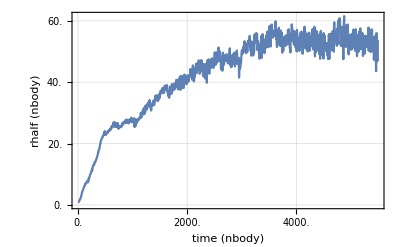

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

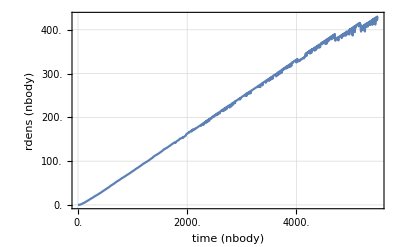

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

2.29269

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	If[$SAVEMXQ,
		Print["Saving data to MX ... "];
		Print[TimeAndMem[]];
		DumpSave["particles.mx", particles];
		Print[TimeAndMem[]];
	];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

14:36:33 mem:168.936MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-100/

DIR: ./run-102/

DIR: ./run-108/

DIR: ./run-111/

DIR: ./run-113/

DIR: ./run-119/

DIR: ./run-124/

DIR: ./run-129/

DIR: ./run-132/

DIR: ./run-142/

DIR: ./run-148/

DIR: ./run-152/

DIR: ./run-163/

DIR: ./run-167/

DIR: ./run-170/

DIR: ./run-172/

DIR: ./run-177/

DIR: ./run-17/

DIR: ./run-184/

DIR: ./run-191/

DIR: ./run-194/

DIR: ./run-195/

DIR: ./run-198/

DIR: ./run-201/

DIR: ./run-206/

DIR: ./run-208/

DIR: ./run-212/

DIR: ./run-214/

DIR: ./run-215/

DIR: ./run-21/

DIR: ./run-101/

DIR: ./run-107/

DIR: ./run-10/

DIR: ./run-112/

DIR: ./run-117/

DIR: ./run-122/

DIR: ./run-125/

DIR: ./run-130/

DIR: ./run-140/

DIR: ./run-144/

DIR: ./run-150/

DIR: ./run-159/

DIR: ./run-166/

DIR: ./run-16/

DIR: ./run-171/

DIR: ./run-174/

DIR: ./run-178/

DIR: ./run-182/

DIR: ./run-189/

DIR: ./run-192/

Closing kernels ...

{212.778,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

14:40:05 mem:10.0057GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 10.0057GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

50

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{50,1100}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,50}

```mathematica
Length/@particles[[4]]//Union
```

{1098,1099,1100}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{1100,1100,1098,1100,1100,1100,1099,1100,1100,1100,1099,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1099,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1099,1100,1099,1100,1098,1100,1100,1100,1100}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{{3},{7},{11},{23},{42},{44},{46}}

```mathematica
delPos1//Length
```

7

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{./run-102/,./run-111/,./run-119/,./run-152/,./run-195/,./run-201/,./run-208/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{run-102,run-111,run-119,run-152,run-195,run-201,run-208}

```mathematica
dirsToDelete//Length
```

7

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{Null,Null,Null,Null,Null,Null,Null}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,50}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,43,1100}

```mathematica
nbIndexes//Length
```

43

```mathematica
parameters//Dimensions
```

{43,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 8.94857GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,43,1100,700}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

CERO AT: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

CERO AT: 10

run: 11

run: 12

CERO AT: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

CERO AT: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

run: 33

run: 34

run: 35

run: 36

run: 37

run: 38

run: 39

run: 40

run: 41

run: 42

run: 43

{1610.5,Null}

```mathematica
ceros[[2]]
```

{{{1,329},{10,1077},{12,321},{25,359}}}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{{1},{10},{12},{25}}

```mathematica
Extract[dirs,delPos2]
```

{./run-100/,./run-124/,./run-129/,./run-170/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{run-100,run-124,run-129,run-170}

```mathematica
dirsToDelete//Length
```

4

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

39

```mathematica
particles//Dimensions
```

{4,43,1100}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,39,1100}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 8.11611GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

39

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100,1100}

```mathematica
parameters//Dimensions
```

{43,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{39,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{1,10},{3,130},{3,131},{3,132},{3,133},{3,134},{3,135},{3,136},{3,137},{3,138},{3,139},{3,140},{3,141},{3,142},{3,143},{3,144},{3,145},{3,146},{3,147},{3,148},{3,149},{3,150},{3,151},{3,152},{3,153},{3,154},{3,155},{3,156},{3,157},{3,158},{3,159},{3,160},{3,161},{3,162},{3,163},{3,164},{3,165},{3,166},{3,167},{3,168},{3,169},{3,170},{3,171},{3,172},{3,173},{3,174},{3,175},{3,176},{3,177},{3,178},{3,179},{3,180},{3,181},{3,182},{3,183},{3,184},{3,185},{3,186},{3,187},{3,188},{3,189},{3,190},{3,191},{3,192},{3,193},{3,194},{3,195},{3,196},{3,197},{3,198},{3,199},{3,200},{3,201},{3,202},{3,203},{3,204},{3,205},{3,206},{3,207},{3,208},{3,209},{3,210},{3,211},{3,212},{3,213},{3,214},{3,215},{3,216},{3,217},{3,218},{3,219},{3,220},{3,221},{3,222},{3,223},{3,224},{3,225},{3,226},{3,227},{3,228},{3,229},{3,230},{3,231},{3,232},{3,233},{3,234},{3,235},{3,236},{3,237},{3,238},{3,239},{3,240},{3,241},{3,242},{3,243},{3,244},{3,245},{3,246},{3,247},{3,248},{3,249},{3,250},{3,251},{3,252},{3,253},{3,254},{3,255},{3,256},{3,257},{3,258},{3,259},{3,260},{3,261},{3,262},{3,263},{3,264},{3,265},{3,266},{3,267},{3,268},{3,269},{3,270},{3,271},{3,272},{3,273},{3,274},{3,275},{3,276},{3,277},{3,278},{3,279},{3,280},{3,281},{3,282},{3,283},{3,284},{3,285},{3,286},{3,287},{3,288},{3,289},{3,290},{3,291},{3,292},{3,293},{3,294},{3,295},{3,296},{3,297},{3,298},{3,299},{3,300},{3,301},{3,302},{3,303},{3,304},{3,305},{3,306},{3,307},{3,308},{3,309},{3,310},{3,311},{3,312},{3,313},{3,314},{3,315},{3,316},{3,317},{3,318},{3,319},{3,320},{3,321},{3,322},{3,323},{3,324},{3,325},{3,326},{3,327},{3,328},{3,329},{3,330},{3,331},{3,332},{3,333},{3,334},{3,335},{3,336},{3,337},{3,338},{3,339},{3,340},{3,341},{3,342},{3,343},{3,344},{3,345},{3,346},{3,347},{3,348},{3,349},{3,350},{3,351},{3,352},{3,353},{3,354},{3,355},{3,356},{3,357},{3,358},{3,359},{3,360},{3,361},{3,362},{3,363},{3,364},{3,365},{3,366},{3,367},{3,368},{3,369},{3,370},{3,371},{3,372},{3,373},{3,374},{3,375},{3,376},{3,377},{3,378},{3,379},{3,380},{3,381},{3,382},{3,383},{3,384},{3,385},{3,386},{3,387},{3,388},{3,389},{3,390},{3,391},{3,392},{3,393},{3,394},{3,395},{3,396},{6,83},{6,84},{8,218},{8,219},{8,352},{8,511},{8,512},{8,513},{8,514},{8,515},{8,516},{8,517},{8,518},{8,853},{9,52},{11,164},{13,4},{13,81},{14,310},{14,364},{14,365},{14,366},{14,367},{14,368},{18,11},{18,23},{21,421},{22,9},{24,5},{29,40},{31,457},{31,458},{31,459},{31,460},{31,461},{31,462},{31,463},{31,464},{31,465},{31,466},{31,467},{31,468},{31,469},{31,470},{31,471},{31,472},{32,227},{33,499},{33,500},{33,501},{33,502},{33,503},{37,660},{39,367},{39,368},{39,369},{39,370},{39,371},{39,372},{39,373},{39,374},{39,375},{39,376},{39,377},{39,378},{39,379},{39,380},{39,556},{39,557},{39,558},{39,559},{39,560},{39,561},{39,562},{39,563},{39,564},{39,565},{39,566},{39,567},{39,568},{39,569},{39,570},{39,571},{39,572},{39,598},{39,599},{39,600},{39,601},{39,602},{39,603},{39,604},{39,605},{39,606},{39,607},{39,608},{39,609},{39,610},{39,611},{39,612},{39,613},{39,614},{39,615},{39,616},{39,617},{39,618},{39,619},{39,620},{39,621},{39,622},{39,623},{39,624},{39,625},{39,626},{39,627},{39,628},{39,629}}

```mathematica
delPos4[[All,1]]//Union
```

{1,3,6,8,9,11,13,14,18,21,22,24,29,31,32,33,37,39}

```mathematica
delPos4[[All,1]]//Union//Length
```

18

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{2,4,5,7,10,12,15,16,17,19,20,23,25,26,27,28,30,34,35,36,38}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{2,4,5,7,10,12,15,16,17,19,20,23,25,26,27,28,30,34,35,36,38}

```mathematica
bad=Partition[delPos4[[All,1]]//Union,1];
good=Partition[Position[moreIDS,{}]//Flatten,1];
```

```mathematica
Write[logstream,"bad runs: ",bad]
```

```mathematica
Write[logstream,"good runs: ",good]
```

```mathematica
badRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,bad],All,2]
```

{run-101,run-108,run-113,run-122,run-125,run-132,run-142,run-144,run-163,run-16,run-171,run-174,run-184,run-191,run-192,run-194,run-214,run-21}

```mathematica
goodRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,good],All,2]
```

{run-107,run-10,run-112,run-117,run-130,run-140,run-148,run-150,run-159,run-166,run-167,run-172,run-177,run-178,run-17,run-182,run-189,run-198,run-206,run-212,run-215}

```mathematica
If[!DirectoryQ["good-runs"],CreateDirectory["./good-runs"]];
If[!DirectoryQ["bad-runs"],CreateDirectory["./bad-runs"]];
```

```mathematica
CopyDirectory[#,"./good-runs/"<>#]&/@goodRunsDirs;
CopyDirectory[#,"./bad-runs/"<>#]&/@badRunsDirs;
```

```mathematica
DeleteDirectory[goodRunsDirs,DeleteContents->True];
DeleteDirectory[badRunsDirs,DeleteContents->True];
```

## Close

```mathematica
(*Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]*)
```

```mathematica
Write[logstream, "End succesfully ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus700.log